```mathematica
ClearAll["Global`*"];
```

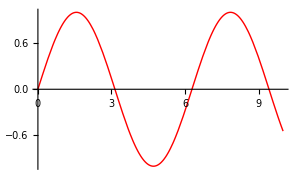
-Graphics--Graphics-

```mathematica
image=ImageResize[ExampleData[{"TestImage","Tiffany"}],300];
Overlay[{ImageAdjust[image,{0,0.5}],Panel[Plot[Sin[x],{x,0,10},PlotStyle->{Thick,Red},ImageSize->ImageDimensions[image]],Alignment->Center,ImageSize->ImageDimensions[image]]}]
```